Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 10 Adams-Moulton method
Solve the initial value problem by Adams-Moulton (7a), (7b), 10 steps with 1 correction per step. Solve exactly and compute the error. Use RK where no starting values are given.

1. y'[x] == y, y[0] == 1, h = 0.1, (1.105171, 1.221403, 1.349858)

Using the same settings for NDSolve here as were used in section 21.1, problem 15. It is not Adams-Moulton, but the automatically adaptive calculation strategy which NDSolve performs by default. Green cells indicate that all equations solutions were retrieved as equal to the text answer.

```mathematica
Clear["Global`*"]
```

```mathematica
s1=DSolve[{y'[x]==y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^x}}

```mathematica
p1=Plot[y[x]/.s1,{x,-1,4},PlotStyle->{Blue,Thickness[0.008]}];
```

```mathematica
s2=NDSolve[{y'[x]==y[x],y[0]==1},y,{x,-1,4},AccuracyGoal->∞,PrecisionGoal->20,WorkingPrecision->35]
```

{{y→InterpolatingFunction[{{-1.0000000000000000000000000000000000, 4.0000000000000000000000000000000000}}, <>]}}

```mathematica
p2=Plot[y[x]/.s2,{x,-1,4},PlotStyle->{White,Thickness[0.004]}];
```

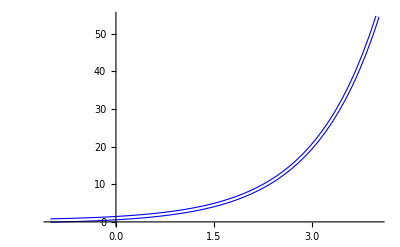

```mathematica
Show[p1,p2]
```

The agreement between the two functions seems to be at least 9S. The enhancement options make a difference. For example, when Precision Goal was 10 and Working Precision was 15, then only 7S was achieved.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,-1,4,0.4}]]
```

{{0.36787944},{0.36787944}}
{{0.54881164},{0.54881164}}
{{0.81873075},{0.81873075}}
{{1.22140280},{1.22140280}}
{{1.82211880},{1.82211880}}
{{2.71828180},{2.71828180}}
{{4.05520000},{4.05520000}}
{{6.04964750},{6.04964750}}
{{9.02501350},{9.02501350}}
{{13.46373800},{13.46373800}}
{{20.08553700},{20.08553700}}
{{29.96410000},{29.96410000}}
{{44.70118400},{44.70118400}}

3.  y'[x]==1+y[x]^2, y[0]==0, h=0.1, (0.100335, 0.202710, 0.309336)

```mathematica
Clear["Global`*"]
```

```mathematica
s1=DSolve[{y'[x]==1+y[x]^2, y[0]==0},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→Tan[x]}}

```mathematica
p1=Plot[y[x]/.s1,{x,-1.4,1.4},PlotStyle->{Red,Thickness[0.008]}];
```

There are developments here with s2. In this case the AccuracyGoal cannot be ∞, because then Mathematica finds a 1/0 condition. PrecisionGoal and WorkingPrecision cannot be sky high without error messages, but as they are set below, they are plenty high enough.

```mathematica
s2=NDSolve[{y'[x]==1+y[x]^2, y[0]==0},y,{x,-1.4,1.4},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->20]
```

{{y→InterpolatingFunction[{{-1.3999999999999999112, 1.3999999999999999112}}, <>]}}

```mathematica
p2=Plot[y[x]/.s2,{x,-1.4,1.4},PlotStyle->{White,Thickness[0.004]}];
```

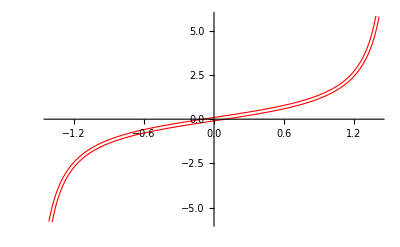

```mathematica
Show[p1,p2]
```

Agreement in the tables between the two solving methods seems to be at least S9.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,-1.4,1.4,0.3}]]
```

{{-5.79788370},{-5.79788370}}
{{-1.96475970},{-1.96475970}}
{{-1.02963860},{-1.02963860}}
{{-0.54630249},{-0.54630249}}
{{-0.20271004},{-0.20271004}}
{{0.10033467},{0.10033467}}
{{0.42279322},{0.42279322}}
{{0.84228838},{0.84228838}}
{{1.55740770},{1.55740770}}
{{3.60210240},{3.60210240}}

5.  Do problem 3 by RK

Problem 3 is already as RK as it’s going to get.

7.  y'[x]==3 y[x]-12 y^2, y[0]==0.2, h=0.1

```mathematica
Clear["Global`*"]
```

```mathematica
s1=DSolve[{y'[x]==3 y[x]-12 y[x]^2, y[0]==0.2},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→ⅇ^(3 x)/(1+4 ⅇ^(3 x))}}

```mathematica
p1=Plot[y[x]/.s1,{x,-1.4,1.4},PlotStyle->{Orange,Thickness[0.008]}];
```

```mathematica
s2=NDSolve[{y'[x]==3 y[x]-12 y[x]^2, y[0]==0.2},y,{x,-1.4,1.4},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->20]
```

NDSolve::precw: The precision of the differential equation ({{y'[x]==3 y[x]-12 y[x]^2,y[0]==0.2},{},{},{},{}}) is less than WorkingPrecision (20.).

{{y→InterpolatingFunction[{{-1.3999999999999999112, 1.3999999999999999112}}, <>]}}

```mathematica
p2=Plot[y[x]/.s2,{x,-1.4,1.4},PlotStyle->{White,Thickness[0.004]}];
```

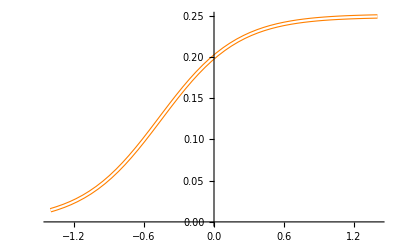

```mathematica
Show[p1,p2]
```

Although Mathematica shows a note deprecating its WorkingPrecision, the results look good to me.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,-1.4,1.4,0.3}]]
```

{{0.01414701},{0.01414701}}
{{0.03214128},{0.03214128}}
{{0.06656382},{0.06656382}}
{{0.11790104},{0.11790104}}
{{0.17175878},{0.17175878}}
{{0.21093405},{0.21093405}}
{{0.23249357},{0.23249357}}
{{0.24257382},{0.24257382}}
{{0.24692656},{0.24692656}}
{{0.24874125},{0.24874125}}

9.  y'[x]==3 x^2(1 +y[x]), y[0]==0, h=0.05

```mathematica
Clear["Global`*"]
```

```mathematica
s1=DSolve[{y'[x]==3 x^2(1 +y[x]), y[0]==0},y[x],x]
```

{{y[x]→-1+ⅇ^(x^3)}}

In the plot I try to capture all the parts of the function which are interesting.

```mathematica
p1=Plot[y[x]/.s1,{x,-1.6,1.4},PlotStyle->{Brown,Thickness[0.008]}];
```

```mathematica
s2=NDSolve[{y'[x]==3 x^2(1 +y[x]), y[0]==0},y,{x,-1.6,1.4},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->20]
```

{{y→InterpolatingFunction[{{-1.6000000000000000888, 1.3999999999999999112}}, <>]}}

```mathematica
p2=Plot[y[x]/.s2,{x,-1.6,1.4},PlotStyle->{White,Thickness[0.004]}];
```

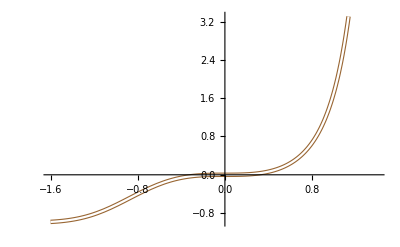

```mathematica
Show[p1,p2]
```

The usual excellent agreement fills the table.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,-1.6,1.4,0.3}]]
```

{{-0.98336090},{-0.98336090}}
{{-0.88886393},{-0.88886393}}
{{-0.63212056},{-0.63212056}}
{{-0.29036179},{-0.29036179}}
{{-0.06199500},{-0.06199500}}
{{-0.00099950},{-0.00099950}}
{{0.00803209},{0.00803209}}
{{0.13314845},{0.13314845}}
{{0.66862511},{0.66862510}}
{{2.78482630},{2.78482630}}
{{14.54905700},{14.54905700}}